Interpolation::inhr: Requested order is too high; order has been reduced to {1}.

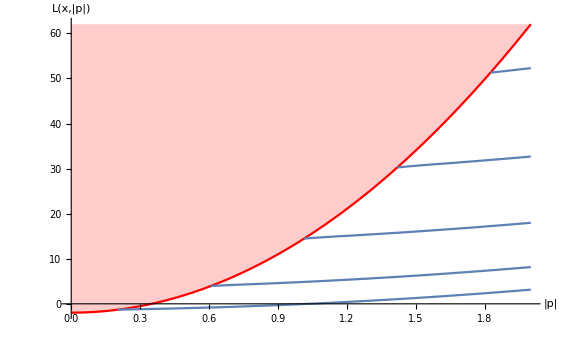

```mathematica
SubMinus[c] = 6000.;
SubPlus[c]  = 1500;
SubMinus[ρ] = 3100.;
SubPlus[ρ] = 1000.;
ω = 2100.;

a = (SubMinus[ρ]/SubPlus[ρ])^2;
b = (SubPlus[c]/SubMinus[c])^2;
p0 =√(ω^2/SubPlus[c]^2) ;

nmax = 4;

minval[n_] := First[FindMinimum[{t^2(a (Cot[t])^2 + b), 3.142 (n - 1) ≤ t ≤ 3.141 n},{t, 3.14 n}]];
dmin = √(minval[nmax] / p0^2(1 - b)) + Pi/2;
d[x1_] := dmin +ArcTan[x1];

q[x1_, p_, n_] := t /.FindRoot[{t^2 (a (Cot[t])^2 + b)== (d[x1])^2 p^2 (1 - b)}, {t, 3.14 n, 3.142 (n - 1), 3.141 n}]

xLeft = -10.;
xMid = 0.;
xRight =  10.;
pMax = 2.;

pMin[x_, n_] := √(minval[n]/((d[x])^2 (1 - b)));
qTab[x_, n_] := Table[{p, q[x, p, n]}, {p, pMin[x, n], pMax, 0.1}];
qFunc[x_, n_] := Interpolation[qTab[x, n]];

(*LLeft[p_] := (c_+)^2((qLeftFunc[p]/d[xLeft])^2 + p^2) - ω^2;*)
ReducedLLeft[p_, n_] := (((qFunc[xLeft, n][p])/d[xLeft])^2 + p^2) - p0^2;

Show[{Plot[1/b p^2-p0^2, {p, 0, pMax}, PlotStyle -> Red, Filling->Top, Ticks->None, AxesLabel->{Style["|p|", FontSize->26],Style["L(x,|p|)", FontSize->26]}],
Plot[ReducedLLeft[p, 1], {p, pMin[xLeft, 1], pMax}], 
Plot[ReducedLLeft[p, 2], {p, pMin[xLeft, 2], pMax}], 
Plot[ReducedLLeft[p, 3], {p, pMin[xLeft, 3], pMax}],
Plot[ReducedLLeft[p, 4], {p, pMin[xLeft, 4], pMax}],
Plot[ReducedLLeft[p, 5], {p, pMin[xLeft, 5], pMax}]}]
```